### Supplemental Notebook

Abstract: In this Notebook, we provide the details of evaluating the Mean First-Passage Time for a four state Chiral Run-and-Tumble Particle.

## Mean First-Passage Time (MFPT)

We begin directly with Equation [] of the main text as that is precisely when the need for the use of a mathematical software is first felt. We had (υ | ω
-ω | -υ)(A_1
A_2)= (-2/s
-2/s) with

```mathematica
υ := (ⅇ^(-λ L) (-α^2+β^2-β λ))/(β^2-α^2)
ω := (ⅇ^(λ L) (-α^2+β^2+β λ))/(β^2-α^2)
```

```mathematica
λ := √(((α^2-β^2) (γ^2+δ^2))/(β δ))
```

```mathematica
α := -(Γ1+Γ3)/v
β := -(-s-Γ1-Γ3)/v
γ := -(-Γ1+Γ3)/v
δ := -(s+Γ1+2 Γ2+Γ3)/v
```

```mathematica
Res := LinearSolve[{{υ,ω},{-ω,-υ}},{-2/s,-2/s}]
```

The solution of the matrix Equation [28] is a column vector with first entry A_1 and second entry A_2.

```mathematica
A1 := Res[[1]]
A2 := Res[[2]]
```

Using Equations [] and [] of the main text we write

```mathematica
Qneg := A1 ⅇ^(-λ x) + A2 ⅇ^(λ x) 
Qpos := (β λ  (-A1 ⅇ^(-λ x)  + A2 ⅇ^(λ x) ))/(-α^2+β^2)
```

```mathematica
Pneg := -γ*Qneg / δ
Ppos := -α*Qpos / β
```

The first-passage densities associated with each of the possible orientations in Laplace space are

```mathematica
Fl := -s*(Qpos - Qneg) / 2 
Fr := -s*(Qpos + Qneg) / 2 
Fd := -s*(Ppos - Pneg) / 2
Fu := -s*(Ppos + Pneg) / 2
```

{l,r,d,u} are associated to the directions left, right, down and up respectively. As already mentioned in the main text, the resulting expressions for the first-passage distributions are too unwieldy to be written explicitly, we can still make sense of the results in a visual format by plotting the quantities of interest after fixing the numerical values of the parameters of the problem.

```mathematica
v = 1.0
L = 10.0
```

1.

10.

As in the main text, we define a chirality parameter  as the measure of bias in the rates of turning left and right. Since this bias is reflected only in the absolute difference of Γ_1 and Γ_3, we can simply take  or  and set the other of the two equal to one by choosing the appropriate scale. Henceforth, we’ll take

```mathematica
Γ1 = 0.4 
Γ2 = 0.2
Γ3 = 1.0
```

0.4

0.2

1.

As we know, the MFPT is related to the Laplace transform of the first-passage distribution as  . Here we plot the MFPT for a CRTP initially starting in the left direction. We denote the MFPT as Tl.

```mathematica
Tl := -SeriesCoefficient[Fl,{s,0,1}]
```

```mathematica
Tl
```

-2. (-110.-1. x+1. x^2)

```mathematica
TlList := Table[{x,Tl},{x,-L,L,0.1}]
```

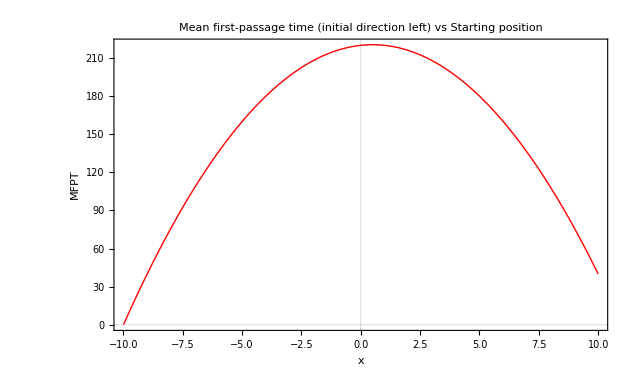

```mathematica
ListLinePlot[TlList,PlotTheme->"Scientific",FrameLabel->{{"MFPT",None},{"x",None}},PlotLabel->"Mean first-passage time (initial direction left) vs Starting position",LabelStyle->{12,GrayLevel[0],Bold},PlotStyle->{Thickness[Large],RGBColor[1,0,0]}]
```

The data can also be exported as CSV file

```mathematica
(*Export["Tlplot",TlList,"CSV"]*)
```

Tlplot

To plot the behaviour of the MFPT while varying one parameter one can generate a list of equally spaced value of that parameter as shown

```mathematica
(*linearmesh[m_,n_,N_Integer]:=Array[#&,N,{m,n}]
ϵlist  := linearmesh[0.0,1.0,11]*)
```

Alternately, one can also manually enter values to be used of this varying parameter and generate the data to be plotted using a For loop

```mathematica
Γ1list := {1/10,3/10,42/100,6/10,8/10,10/10}
```

```mathematica
For[i=1;empty = {},i≤ Length[Γ1list],i++,Γ1 = Γ1list[[i]];Tl := -SeriesCoefficient[Fl,{s,0,1}];TlList := Table[{x,Tl},{x,-L,L,0.1}]; AppendTo[empty,TlList]]
```

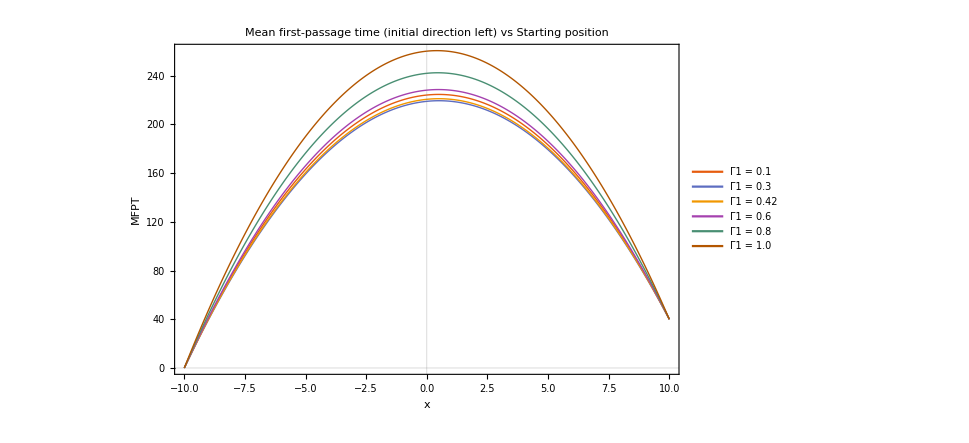

```mathematica
ListLinePlot[empty,PlotTheme->"Scientific",FrameLabel->{{"MFPT",None},{"x",None}},PlotLabel->"Mean first-passage time (initial direction left) vs Starting position",LabelStyle->{12,GrayLevel[0],Bold},PlotStyle->{Thickness[Large]},PlotLegends->{"Γ1 = 0.1","Γ1 = 0.3","Γ1 = 0.42","Γ1 = 0.6","Γ1 = 0.8","Γ1 = 1.0"}]
```

As is clearly shown in the plot above, the MFPT to reach either of the two absorbing boundaries at  is minimized for every starting position  for a specific value of Γ_1. To further aid visualization, we can plot the maximum value that the MFPT attains for a specific value of Γ_1 against Γ_1.

```mathematica
For[i=1;empty1 = {},i≤ Length[Γ1list],i++,maxl := Max[empty[[i]]]; AppendTo[empty1,maxl]]
```

```mathematica
data := Transpose@{Γ1list,empty1}
```

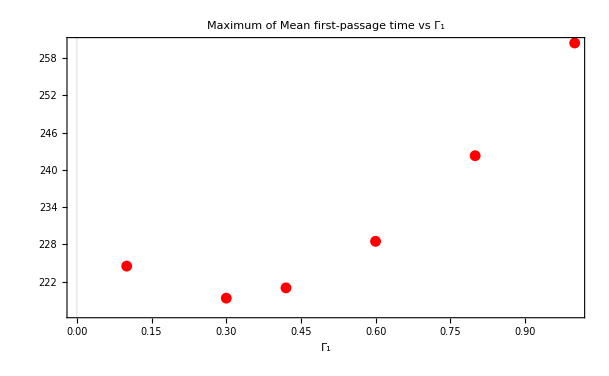

```mathematica
ListPlot[data,PlotTheme->"Scientific",FrameLabel->{{"",None},{"Γ_1",None}},PlotLabel->"Maximum of Mean first-passage time vs Γ_1",LabelStyle->{12,GrayLevel[0],Bold},PlotStyle->{Thickness[Large],RGBColor[1,0,0]}]
```